```mathematica
fsz=22;16;
(*path=NotebookDirectory[]<>"figures/"*)
fontFamilyPB="Latin Modern Math";"Helvetica";
fontFamily="Times New Roman";FontSize->24;

SetOptions[Plot,BaseStyle->{FontFamily->fontFamily,FontSize->fsz}];
SetOptions[ListPlot,BaseStyle->{FontFamily->fontFamily,FontSize->fsz}];
SetOptions[ListLogPlot,BaseStyle->{FontFamily->fontFamily,FontSize->fsz}];
SetOptions[ListLogLinearPlot,BaseStyle->{FontFamily->fontFamily,FontSize->fsz}];
SetOptions[ListLogLogPlot,BaseStyle->{FontFamily->fontFamily,FontSize->fsz}];
SetOptions[Graphics,BaseStyle->{FontFamily->fontFamily,FontSize->fsz}];

PPlot[sol_]:= Module[{lineStyle,pltStl,thickness},
lineStyle=Dashing[{1,0}];Automatic;xRPlotMin=0;ar=1;gridLines=Automatic;imSz=400;
pltStl={{lineStyle,Blue,Thickness[thickness=.013/2]},{lineStyle,RGBColor[0.7,0.3,0.0],Thickness[thickness]},{lineStyle,RGBColor[0.9,0.5,0.6],Thickness[thickness]},{lineStyle,Brown,Thickness[thickness]},{lineStyle,Black,Thickness[thickness]}};
Plot[Evaluate[{O2[t],CH[t]}/.sol],{t,0,Tmax}(*,PlotRange->All*),(*PlotLegends->Placed[{"g GL_ij","g (H-ω)^-1","ψ_j"},{.65,.5}],*)PlotRange->{{0,Tmax},{0,7}},AspectRatio->1,(*ImageSize->250,*)FrameLabel->{"Time","Amount"},
PlotLegends->Placed[{Style["O_2",FontSize->fsz,FontFamily->fontFamily],Style["CH_4",FontSize->fsz,FontFamily->fontFamily],Style["CO_2",FontSize->fsz,FontFamily->fontFamily]},{0.45,0.85}],ImageSize->imSz,Axes->None,PlotStyle->pltStl,Frame->True,BaseStyle->{FontFamily->"Times New Roman",FontSize->fsz},FrameStyle->Thick,FrameTicksStyle->Black,LabelStyle->Black,GridLines->gridLines,AspectRatio->ar
]
];
```

```mathematica
Clear[F,B,O2,B0,C0,Func,M];
```

```mathematica
Func:=Module[{f,g,eqs,BC,DEq,sol},
f=HeavisideTheta[R[t]-R0]α A[t](R[t]-R0);
g=ϵ A[t]R[t]HeavisideTheta[R1-R[t]]+ϵ A[t] R1 HeavisideTheta[R[t]-R1];

eqs={R'[t] == -f-g+σ1,
G'[t]== ((1-ξ)ω R[t] - a1) G[t],
H'[t]==  ((1-ψ)Ω CH[t] - a2) H[t],
L'[t]== f - β B[t] L[t]+ξ ω R[t] G[t],
CO'[t]==μ O2[t] g + γ λ O2[t] CH[t] F[t]+ψ Ω CH[t] H[t],
CH'[t] == κ β B[t] L[t] - γ O2[t] CH[t] F[t],
O2'[t] == -(μ O2[t] g + γ λ O2[t] CH[t] F[t])+σ2,
A'[t] == (1-μ)O2[t]g - s A[t],
B'[t]==((1-κ) β L[t] -u) B[t],
F'[t] == ((1-λ)γ O2[t] CH[t]-ν)F[t]};
BC = {R[0]==RI,L[0]==0,CO[0]==0,CH[0]==0,A[0]==A0,B[0]==B0,F[0]==C0,O2[0]==O20,G[0]==G0,H[0]==H0};
DEq = Flatten[{eqs,BC}];

sol=NDSolve[DEq,{A,B,F,O2',CH',L',CO',R',O2,CH,L,CO,R,G,H},{t,0,Tmax}];
First[sol]
(*{Plot[Evaluate[{F[t],B[t],A[t]}/.sol],{t,0,Tmax},PlotRange->PR,PlotLegends->{"F","B","A"}],
Plot[Evaluate[{O2'[t],CH'[t],L'[t],CO'[t],R'[t]}/.sol],{t,0,Tmax},PlotRange->All,PlotLegends->{"O2","CH4","Lac","CO2","R"}],
Plot[Evaluate[{O2[t],CH[t],L[t],CO[t],R[t]}/.sol],{t,0,Tmax},PlotRange->All,PlotLegends->{"O2","CH4","Lac","CO2","R"}]
};*)
]
```

```mathematica
R0=2.5;
R1=1;

a2 = 0.5;
a1=0.5; (* 0.1  *)
s=0.1;
ν=0.1;
u=0.1;

λ=0.5; 
κ=0.5;
μ=0.5;
ξ=0.5; (* 0.5 *)
ψ=0.5;

A0=1.;
H0=1; (*1? *)
G0=1;
B0=1;
C0=1;

β=0.5; 
α=0.5; (* 0.5 *)
ω=0.02; (* 0.02 *)
Ω=0.02;
ϵ=0.5;
γ=0.5;
```

#### Oscillation qualitative analysis

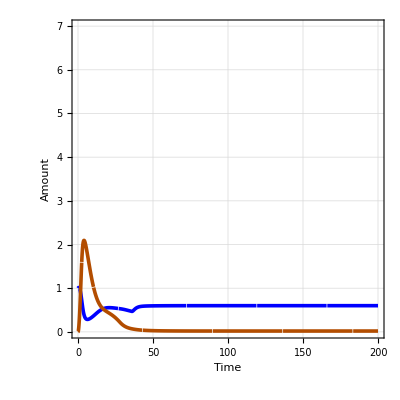

```mathematica
RI=10;
O20=1;
σ1 = 1; (* resource rate  0.8*)
σ2 = 0.3; (* oxygen rate 0.15 *)
Tmax =200;
sol  = Func;
tx = 97;
(*HeavisideTheta[R[tx]-R0]α A[tx](R[tx]-R0)/.sol
- β B[tx] L[tx]+ξ ω R[tx] G[tx] /.sol 
(*$Assumptions=e>0 && σ >0 && c>0;
Simplify[X[t]/.DSolve[{X'[t]==(c (R+σ (t-t0)) - a)X[t],X[t0]==e},X,t][[1]]]*)
(*$Assumptions=k>0;
DSolve[{L'[t]== f- β B[t] L[t],B'[t]==((1-κ) β L[t] -u) B[t]},{L,B},t]*)
Simplify[-L'[t]+ f Exp[I k t]- β B[t] L[t] /. L[t] -> l Exp[I k t+m t +c1]/.L'[t] -> l Exp[I k t+m t +c1] (I k+m)/. B[t] -> b Exp[I k t+n t +c2]]
Simplify[-B'[t]+((1-κ) β L[t] -u) B[t]/. B[t] -> b Exp[I k t+n t +c2]/.B'[t] -> b Exp[I k t+n t +c2] (I k+n)/. L[t] -> l Exp[I k t+m t +c1]]
Solve[{-0.1-ⅈ k+0.25 ⅇ^(c1+ⅈ k t+m t) l-n==0,f-0.5 b ⅇ^(c1+c2+(ⅈ k+m+n) t) l-ⅇ^(c1+m t) l (ⅈ k+m)},k]*)
(*DSolve[{B'[t]==((1-k) b L[t] -U) B[t],L'[t]== α A[t](σ2 t+R) - β B[t] L[t],A'[t] == (1-μ)O2[t]ϵ A[t] R1 - s A[t]},{B,L,A,O2},t]*)
PPlot[sol]
```

```mathematica
γ λ
```

0.25

```mathematica
Simplify[t/.Normal[Solve[e ⅇ^(1/2 (t-t0) (-2 a+2 c R+c (t-t0) σ))==1,t][[1]]/.C[1]->0]]
```

(a-c R+c t0 σ-√((a-c R)^2-2 c σ Log[e]))/(c σ)

```mathematica
FullSimplify[Normal[t/.Solve[e ⅇ^(-a t+c R t+1/2 c t^2 σ)==1,t][[1]]]/.C[1]->0]
(a-c R)+Abs[(a- c R)]/.c-> (1-ξ)ω/.a->a1/.R-> 120/.e-> 10^-14/.σ-> 0.5
PowerExpand[-Log[e]/Abs[(a-c R)]/.e-> 10^(-n)]
```

(a-c R+√((a-c R)^2-2 c σ Log[e]))/(c σ)

0.

(n (Log[2]+Log[5]))/Abs[a-c R]

```mathematica
Series[(x+√(x^2-2 c σ Log[e]))/(c σ),{x,Infinity,1}]
```

(2 x)/(c σ)-Log[e]/x+O[1/x]^2

```mathematica
(a-c R+√((a-c R)^2-2 c σ (2 ⅈ π C[1]+Log[e])))/(c σ)a
```

```mathematica
Normal[t/.Solve[e ⅇ^(-a t+c R t+1/2 c t^2 σ)==1,t][[1]]]/.c-> (1-ξ)ω/.a->a1/.R-> 500/.e-> 10^-14/.σ-> 0.5/. C[1]->0
```

7.13531

#### Time of instability analysis

```mathematica
asd
```

#### Part from non-driven - probably not useful here

```mathematica
resO2 = {};
resCO = {};
resCH = {};
Do[
Do[
RI=r;
O20=o;
sol = Func;
o2 = O2[Tmax]/.sol;
co = CO[Tmax]/.sol;
ch = CH[Tmax]/.sol;
tot = o2+co+ch;
(*Print[o2,co,ch];*)
AppendTo[resO2,{r,o,o2/tot}];
AppendTo[resCO,{r,o,co/tot}];
AppendTo[resCH,{r,o,ch/tot}];
,{r,2,12,0.5}],{o,1,12,0.5}];

grph=GraphicsRow[{ListDensityPlot[resO2,PlotTheme->"Detailed",ColorFunction->ColorData["AvocadoColors"],PlotRange->All,FrameLabel-> {"Resource","O_2 [t=0]"},PlotLabel->"O_2 concentration",PlotRange->{0,1},PlotLegends->BarLegend[Automatic,LegendMarkerSize->200],ImageSize->210],
ListDensityPlot[resCO,PlotTheme->"Detailed",ColorFunction->ColorData["AvocadoColors"],PlotRange->All,FrameLabel-> {"Resource","O_2 [t=0]"},PlotLabel->"CO_2 concentration",PlotRange->{0,1},PlotLegends->BarLegend[Automatic,LegendMarkerSize->200],ImageSize->210],ListDensityPlot[resCH,PlotTheme->"Detailed",ColorFunction->ColorData["AvocadoColors"],PlotRange->All,FrameLabel-> {"Resource","O_2 [t=0]"},PlotLabel->"CH_4 concentration",PlotRange->{0,1},PlotLegends->BarLegend[Automatic,LegendMarkerSize->200],ImageSize->210]},Background->White,ImageSize->Full]


(*Plot[Evaluate[{O2[t],CH[t],L[t],CO[t]}/.Func],{t,0,Tmax},PlotRange->All,PlotLegends->{"O_2","CH_4","Lactate","CO_2"},PlotTheme->"Detailed",FrameTicks-> {{{0},None},{{0},None}},FrameLabel-> {Style["Time",16,Black],Style["Quantity",16,Black]}]*)
```

-Graphics-